## Bootstrapped EWS for Composite EWS using Chlorella and Brachionus

## Setup

```mathematica
SetDirectory["/Users/tbury/Google\ Drive/Research/doctorate/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Job number *)
jobNum=6546;
```

```mathematica
(* Data directory *)
dataDir="hagrid/fussmann_ews/Jobs/job-"<>ToString[jobNum]<>"/";
```

```mathematica
(* Import parameters used *)
pars=Import[dataDir<>"pars.txt","Data"];
```

```mathematica
pars//TableForm
```

span | rw | ham_length | ham_offset | w_cutoff | sweep | block_size | bs_type | n_samples
80 | 1 | 80 | 0.5 | 1 | true | 40 | Circular | 100

```mathematica
(* EWS data *)
ewsRaw=Import[dataDir<>"ews_intervals.csv"];
```

```mathematica
(* bootstraped power spectrumdata *)
pspecBootRaw=Import[dataDir<>"/pspec.csv"];
```

```mathematica
(* power spectrum data *)
pspecChlorRaw=Import["data_export/pspec_chlor.csv"];
pspecBrachRaw=Import["data_export/pspec_brach.csv"];
```

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

### Construct power spectrum data

```mathematica
pspecBootRaw[[2]]
```

{0.04,Brachionus,1,-3.14159,0.084653}

```mathematica
(* bootstrapped data *)
sample=4;
pspecsBootBrach=Table[Cases[pspecBootRaw,{delta,"Brachionus",sample,_,_}][[;;,{4,5}]],{delta,deltaVals}];
pspecsBootChlor=Table[Cases[pspecBootRaw,{delta,"Chlorella",sample,_,_}][[;;,{4,5}]],{delta,deltaVals}];
```

```mathematica
(* original power spectra *)
pspecsBrach=Table[Cases[pspecBrachRaw,{delta,_,_}][[;;,{2,3}]],{delta,deltaVals}];
pspecsChlor=Table[Cases[pspecChlorRaw,{delta,_,_}][[;;,{2,3}]],{delta,deltaVals}];
```

```mathematica
deltaVals
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### General figure parameters

```mathematica
(* Figure params *)
TMBcolours=ColorData[97,"ColorList"];
imgs=400;
colChlor=Black;
colBrach=Pink
```

RGBColor[1, 0.5, 0.5]

```mathematica
aRatio=0.25; (* aspect ratio *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterSize=12;
ltb=0.005; (* line thickness for bifurcation *)
lt=0.005; (* line thickness *)
ls=9; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Power Spectrum Plots

```mathematica
deltaVals
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* Delta values approaching h1 *)
deltaH1={0.04,0.07,0.12,0.32,0.64};
deltaH1index=Position[deltaVals,#]&/@deltaH1//Flatten;
```

```mathematica
(* Delta values approahing h2 *)
deltaH2={1.37,1.24,1.17,0.95,0.69};
deltaH2index=Position[deltaVals,#]&/@deltaH2//Flatten;
```

```mathematica
(* line legend H1 *)
legendH1=LineLegend[Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}],
Style[ToString[#],(ls-1)]&/@deltaH1,
Spacings->{0,-0.1},
LabelStyle->ls,
LegendLabel->"δ"]
```

```mathematica
(* line legend H2 *)
legendH2=LineLegend[Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}],
Style[ToString[#],(ls-1)]&/@deltaH2,
Spacings->{0,-0.1},
LabelStyle->ls,
LegendLabel->"δ"]
```

### Chlorella approach H1

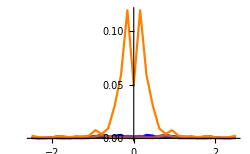

```mathematica
(* Chlorella approach H1 *)
ListLinePlot[Table[pspecsChlor[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

### Chlorella approach H2

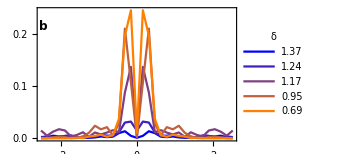

```mathematica
(* Chlorella approach H2 *)
plotPspecChlorH2=ListLinePlot[Table[pspecsChlor[[i]],{i,deltaH2index}],
LabelStyle->ls,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}],
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{Automatic,Range[0,1,0.1]},{Automatic,Automatic}},
FrameTicksStyle->{{FontOpacity->0,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->250,
PlotLegends->Placed[legendH2,Scaled[{0.83,0.65}]],
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}]
```

### Brachionus approach H1

```mathematica
(* bar legend *)
barLegendH1=BarLegend[{Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}]},deltaH2,LegendLabel->"δ",LegendMarkerSize->150]
```

BarLegend[{{RGBColor[0, 0, 1],RGBColor[Rational[1, 4], 0.125, Rational[3, 4]],RGBColor[Rational[1, 2], 0.25, Rational[1, 2]],RGBColor[Rational[3, 4], 0.375, Rational[1, 4]],RGBColor[1, 0.5, 0]}},{1.37,1.24,1.17,0.95,0.69},LegendLabel→δ,LegendMarkerSize→150]

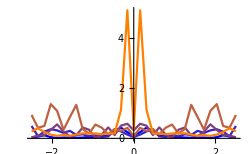

```mathematica
(* Brachionus approach H1 *)
ListLinePlot[Table[pspecsBrach[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

### Brachionus approach H2

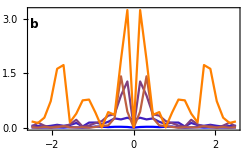

```mathematica
(* Brachionus approach H2 *)
plotPspecBrachH2=ListLinePlot[Table[pspecsBrach[[i]],{i,deltaH2index}],
LabelStyle->ls,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}],
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Frequency, ω",""}},
FrameTicks->{{Automatic,Range[0,3,1]},{Automatic,Automatic}},
FrameTicksStyle->{{FontOpacity->0,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->250,
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}]
```

### Combine

```mathematica
widthPspec=5cm;
heightPspec=2.5cm;
```

```mathematica
pspecGrid=Graphics[{
Inset[Show[plotPspecBrachH2,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthPspec+leftPad+rightPad,heightPspec+bottomPad}],
Inset[Show[plotPspecChlorH2,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{0,topPad}}],{0,bottomPad+heightPspec+gapVert},{Left,Bottom},{widthPspec+leftPad+rightPad,heightPspec+topPad}]
},
ImageSize->{widthPspec+leftPad+rightPad,bottomPad+heightPspec*2+gapVert+topPad}
]
```

-Graphics-

```mathematica
Inset[Show[aicPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}]
```

Show::gtype: Symbol is not a type of graphics.

Inset[Show[aicPlotComp,AspectRatio→Full,ImagePadding→{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{leftPad+rightPad+widthFig,bottomPad+heightFig}]

## Bifurcation diagram

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsChlor=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsChlor]}];
bifPtsBrach=Table[DeleteCases[bifPtsBrach[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsBrach]}];
```

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=0.32;
expBif1b=0.64;
expBif2=1.16;
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* Legend *)
legend=LineLegend[{colChlor,colBrach},{Style["Chlorella vulgaris",ls-1,Italic],Style["Brachionus calyciflorus",ls-1,Italic]},Spacings->{0,0.2}]
```

```mathematica
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[ltb]},{i,1,Length[bifPtsChlor]}],
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,6}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,6]*1000000,Range[0,6]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
PlotLegends->Placed[legend,Scaled[{0.79,0.85}]],
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",labelLetterSize,Bold],labelLetterPos]}];
```

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-64/40,64}},
PlotStyle->Table[{colBrach,Thickness[ltb]},{i,1,Length[bifPtsBrach]}],
LabelStyle->ls,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False];
```

```mathematica
Graphics[
{Inset[Show[bifPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
Inset[Show[bifPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}]}]
```

-Graphics-

## Plots of EWS against delta

### Variance and Smax

```mathematica
colVar=TMBcolours[[2]];
colSmax=TMBcolours[[3]];
```

```mathematica
(* line legend *)
legend=LineLegend[{colVar,colSmax},{"Variance","S_max"},Spacings->{0,0},LabelStyle->(ls-1)]
```

```mathematica
(* Index of EWS of interest *)
indexVar=Position[ewsRaw[[1]],"Variance"][[1,1]];
indexSmax=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

#### Chlorella

```mathematica
(* Extract confidence intervals for variance of Chlorella *)
lowerVarC=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperVarC=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanVarC=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for smax of Chlorella *)
lowerSmaxC=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSmaxC=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSmaxC=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
varSmaxPlotChlor=ListLinePlot[{lowerVarC,upperVarC,meanVarC,lowerSmaxC,upperSmaxC,meanSmaxC},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
PlotRange->{{0,1.5},{10^(-3.5),2}},
PlotStyle->{{Lighter[colVar,0.5],Thickness[lt]},{Lighter[colVar,0.5],Thickness[lt]},{colVar,Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{colSmax,Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.9,0.85}]],
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
];
```

#### Brachionus

```mathematica
(* Extract confidence intervals for variance of Chlorella *)
lowerVarB=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperVarB=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanVarB=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for smax of Chlorella *)
lowerSmaxB=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSmaxB=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSmaxB=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
varSmaxPlotBrach=ListLinePlot[{lowerVarB,upperVarB,meanVarB,lowerSmaxB,upperSmaxB,meanSmaxB},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
PlotRange->{{0,1.5},{10^(-1.6),10^(1.7)}},
PlotStyle->{{Lighter[colVar,0.5],Thickness[lt]},{Lighter[colVar,0.5],Thickness[lt]},{colVar,Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{colSmax,Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
];
```

#### Composite

```mathematica
(* Compute composite EWS *)
lowerVarComp=Transpose[{lowerVarB[[;;,1]],Mean[{Normalize[lowerVarB[[;;,2]]],Normalize[lowerVarC[[;;,2]]]}]}];
upperVarComp=Transpose[{upperVarB[[;;,1]],Mean[{Normalize[upperVarB[[;;,2]]],Normalize[upperVarC[[;;,2]]]}]}];
meanVarComp=Transpose[{meanVarB[[;;,1]],Mean[{Normalize[meanVarB[[;;,2]]],Normalize[meanVarC[[;;,2]]]}]}];
```

```mathematica
(* Compute composite EWS *)
lowerSmaxComp=Transpose[{lowerSmaxB[[;;,1]],Mean[{Normalize[lowerSmaxB[[;;,2]]],Normalize[lowerSmaxC[[;;,2]]]}]}];
upperSmaxComp=Transpose[{upperSmaxB[[;;,1]],Mean[{Normalize[upperSmaxB[[;;,2]]],Normalize[upperSmaxC[[;;,2]]]}]}];
meanSmaxComp=Transpose[{meanSmaxB[[;;,1]],Mean[{Normalize[meanSmaxB[[;;,2]]],Normalize[meanSmaxC[[;;,2]]]}]}];
```

```mathematica
varSmaxPlotComp=ListLinePlot[{lowerVarComp,upperVarComp,meanVarComp,lowerSmaxComp,upperSmaxComp,meanSmaxComp},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
PlotRange->{{0,1.5},{10^(-1.6),10^(0.2)}},
PlotStyle->{{Lighter[colVar,0.5],Thickness[lt]},{Lighter[colVar,0.5],Thickness[lt]},{colVar,Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{colSmax,Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{{0.05,0.1,0.2,0.4,0.8},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.89,0.8}]],
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
];
```

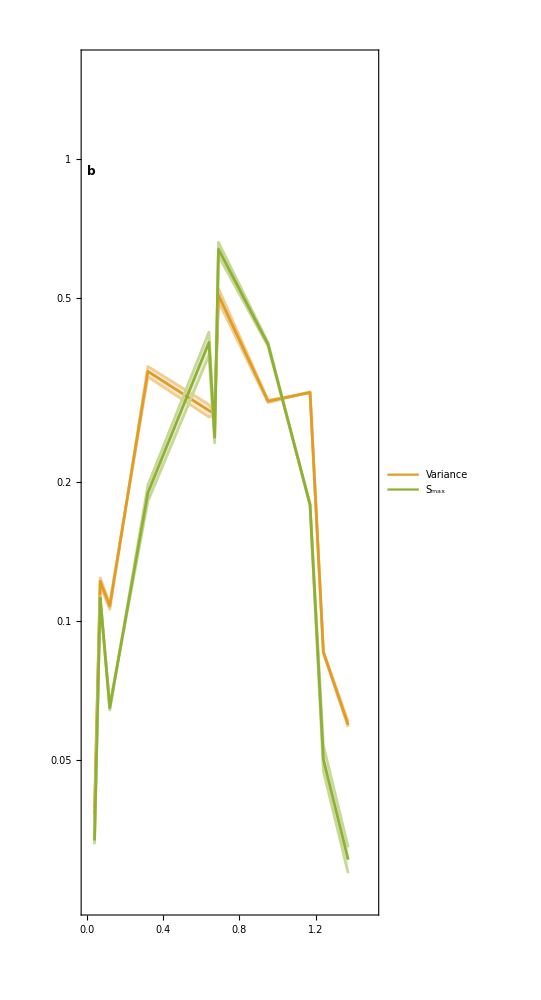

```mathematica
Graphics[Inset[Show[varSmaxPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}]]
```

### Autocorrelation

```mathematica
indexAc1=Position[ewsRaw[[1]],"Lag-1 AC"][[1,1]];
indexAc2=Position[ewsRaw[[1]],"Lag-2 AC"][[1,1]];
indexAc10=Position[ewsRaw[[1]],"Lag-10 AC"][[1,1]];
```

```mathematica
(* figure colours *)
acCols=TMBcolours[[{4,5,7}]]
```

{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
(* line legend *)
legend=LineLegend[acCols,Table["Lag-"<>ToString[i]<>" AC",{i,{1,2,10}}],Spacings->{0,0},LabelStyle->(ls-1)]
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerAc1C=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperAc1C=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanAc1C=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerAc1B=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperAc1B=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanAc1B=Cases[ewsRaw[[2;;,{1,2,3,indexAc1}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerAc1Comp=Transpose[{lowerAc1B[[;;,1]],Mean[{lowerAc1B[[;;,2]],lowerAc1C[[;;,2]]}]}];
upperAc1Comp=Transpose[{upperAc1B[[;;,1]],Mean[{upperAc1B[[;;,2]],upperAc1C[[;;,2]]}]}];
meanAc1Comp=Transpose[{meanAc1B[[;;,1]],Mean[{meanAc1B[[;;,2]],meanAc1C[[;;,2]]}]}];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerAc2C=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperAc2C=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanAc2C=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerAc2B=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperAc2B=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanAc2B=Cases[ewsRaw[[2;;,{1,2,3,indexAc2}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerAc2Comp=Transpose[{lowerAc2B[[;;,1]],Mean[{lowerAc2B[[;;,2]],lowerAc2C[[;;,2]]}]}];
upperAc2Comp=Transpose[{upperAc2B[[;;,1]],Mean[{upperAc2B[[;;,2]],upperAc2C[[;;,2]]}]}];
meanAc2Comp=Transpose[{meanAc2B[[;;,1]],Mean[{meanAc2B[[;;,2]],meanAc2C[[;;,2]]}]}];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerAc10C=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperAc10C=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanAc10C=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerAc10B=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperAc10B=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanAc10B=Cases[ewsRaw[[2;;,{1,2,3,indexAc10}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerAc10Comp=Transpose[{lowerAc10B[[;;,1]],Mean[{lowerAc10B[[;;,2]],lowerAc10C[[;;,2]]}]}];
upperAc10Comp=Transpose[{upperAc10B[[;;,1]],Mean[{upperAc10B[[;;,2]],upperAc10C[[;;,2]]}]}];
meanAc10Comp=Transpose[{meanAc10B[[;;,1]],Mean[{meanAc10B[[;;,2]],meanAc10C[[;;,2]]}]}];
```

```mathematica
acPlotComp=ListLinePlot[{lowerAc1Comp,upperAc1Comp,meanAc1Comp,
lowerAc2Comp,upperAc2Comp,meanAc2Comp,
lowerAc10Comp,upperAc10Comp,meanAc10Comp},
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.6,1.2}},
PlotStyle->{{Thickness[lt],Lighter[acCols[[1]],0.5]},{Thickness[lt],Lighter[acCols[[1]],0.5]},{Thickness[lt],acCols[[1]]},
{Thickness[lt],Lighter[acCols[[2]],0.5]},{Thickness[lt],Lighter[acCols[[2]],0.5]},{Thickness[lt],acCols[[2]]},
{Thickness[lt],Lighter[acCols[[3]],0.5]},{Thickness[lt],Lighter[acCols[[3]],0.5]},{Thickness[lt],acCols[[3]]}},
Filling->{{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
(*FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}}*)
(*FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}}*)
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.88,0.77}]],
Epilog->{Text[Style["c",labelLetterSize,Bold],labelLetterPos]}];
```

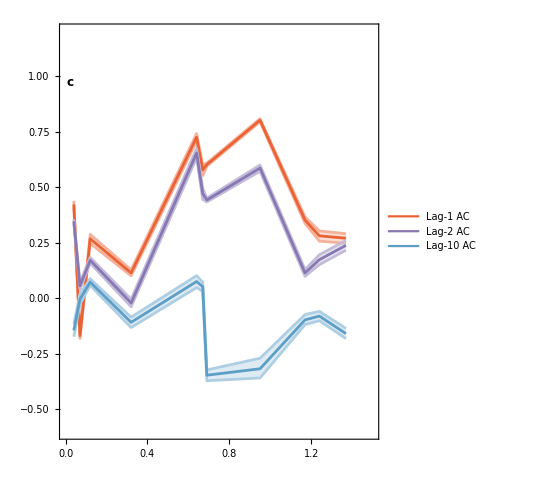

```mathematica
Graphics[Inset[Show[acPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}]]
```

### AIC weights Chlorella

```mathematica
(* figure colours *)
aicCols=TMBcolours[[{15,8,6}]]
```

{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[1, 0.75, 0],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
(* line legend *)
legend=LineLegend[aicCols,{"w_fold","w_hopf","w_null"},Spacings->{0,-0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Index of EWS of interest *)
indexFold=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
indexHopf=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
indexNull=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
aicPlotChlor=ListLinePlot[{lowerFoldC,upperFoldC,meanFoldC,lowerHopfC,upperHopfC,meanHopfC,lowerNullC,upperNullC,meanNullC},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.9,0.8}]],
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}];
```

### AIC weights Brachionus

```mathematica
(* Index of EWS of interest *)
indexFold=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
indexHopf=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
indexNull=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
aicPlotBrach=ListLinePlot[{lowerFoldB,upperFoldB,meanFoldB,lowerHopfB,upperHopfB,meanHopfB,lowerNullB,upperNullB,meanNullB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}];
```

### AIC weights: Composite

```mathematica
(* Compute composite EWS *)
lowerFoldComp=Transpose[{lowerFoldB[[;;,1]],Mean[{lowerFoldB[[;;,2]],lowerFoldC[[;;,2]]}]}];
upperFoldComp=Transpose[{upperFoldB[[;;,1]],Mean[{upperFoldB[[;;,2]],upperFoldC[[;;,2]]}]}];
meanFoldComp=Transpose[{meanFoldB[[;;,1]],Mean[{meanFoldB[[;;,2]],meanFoldC[[;;,2]]}]}];
```

```mathematica
(* Compute composite EWS *)
lowerHopfComp=Transpose[{lowerHopfB[[;;,1]],Mean[{lowerHopfB[[;;,2]],lowerHopfC[[;;,2]]}]}];
upperHopfComp=Transpose[{upperHopfB[[;;,1]],Mean[{upperHopfB[[;;,2]],upperHopfC[[;;,2]]}]}];
meanHopfComp=Transpose[{meanHopfB[[;;,1]],Mean[{meanHopfB[[;;,2]],meanHopfC[[;;,2]]}]}];
```

```mathematica
(* Compute composite EWS *)
lowerNullComp=Transpose[{lowerNullB[[;;,1]],Mean[{lowerNullB[[;;,2]],lowerNullC[[;;,2]]}]}];
upperNullComp=Transpose[{upperNullB[[;;,1]],Mean[{upperNullB[[;;,2]],upperNullC[[;;,2]]}]}];
meanNullComp=Transpose[{meanNullB[[;;,1]],Mean[{meanNullB[[;;,2]],meanNullC[[;;,2]]}]}];
```

```mathematica
aicPlotComp=ListLinePlot[{lowerFoldComp,upperFoldComp,meanFoldComp,lowerHopfComp,upperHopfComp,meanHopfComp,lowerNullComp,upperNullComp,meanNullComp},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.05,1.05}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotLegends->Placed[legend,Scaled[{0.92,0.75}]],
ImageSize->250,
Epilog->{Directive[{Black}],Text[Style["d",labelLetterSize,Bold],labelLetterPos]}];
```

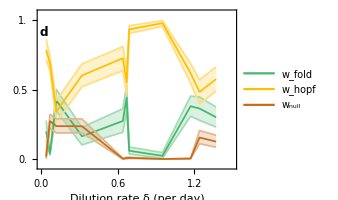

```mathematica
Graphics[Inset[Show[aicPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}]]
```

## Grid all plots together

### Dimensions of Figure

```mathematica
cm=72/2.54;
```

```mathematica
(* Horizontal dimensions *)
leftPad=1.6cm;
widthFig=10cm;
rightPad=1.6cm;
(* Total horizontal dimension *)
imWidth=widthFig+leftPad+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightFig=2.3cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=0.7cm;
(* Total vertical dimension *)
imHeight=3*heightFig+heightBif+3*gapVert+bottomPad+topPad;
imHeight/cm
imWidth/cm
```

13.8

13.2

### Construct figure

```mathematica
lineBase=bottomPad;
lineTop=bottomPad+3*heightFig+heightBif+3*gapVert;
```

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[aicPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}],
(* 2nd row *)
Inset[Show[acPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+heightFig+gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 5th row  *)
Inset[Show[varSmaxPlotComp,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+2*heightFig+2*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 6th (top) row  *)
Inset[Show[bifPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+3*heightFig+3*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
Inset[Show[bifPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+3*heightFig+3*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
(* Grey coloumns and labels *)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{3.8cm,lineBase},{(3.8+2.1)cm,lineTop}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{(9.4+0.05)cm,lineBase},{(9.4-0.05)cm,lineTop}],
Opacity[1],Text[Style["H1",Black,12],{4.9cm,lineTop+0.3cm}],Text[Style["H2",Black,12],{9.4cm,lineTop+0.3cm}]
},
ImageSize->{imWidth,imHeight}
];
```

### Export Figure

```mathematica
plotGrid
```

-Graphics-

```mathematica
(*Export["figures/finals/fussmann_ews_comp.png",plotGrid,ImageResolution->300];*)
```